```mathematica
sol1=Exp[-x^2/4]*Hypergeometric1F1[1/2a+1/4,1/2,1/2x^2]
```

ⅇ^(-x^2/4) Hypergeometric1F1[1/4+a/2,1/2,x^2/2]

```mathematica
sol2=x*Exp[-x^2/4]*Hypergeometric1F1[1/2a+3/4,3/2,1/2x^2]
```

ⅇ^(-x^2/4) x Hypergeometric1F1[3/4+a/2,3/2,x^2/2]

```mathematica
FullSimplify[D[sol1,{x,2}]-(1/4*x^2+a)*sol1]
```

0

```mathematica
FullSimplify[D[sol2,{x,2}]-(1/4*x^2+a)*sol2]
```

0

```mathematica
FunctionExpand[Hypergeometric1F1[-m^2/4+1/4,1/2,m^2 x^2]]
```

Hypergeometric1F1[1/4-m^2/4,1/2,m^2 x^2]

```mathematica
realsol1=Exp[-m^2 x^2/2]*Hypergeometric1F1[-m^2/4+1/4,1/2,m^2 x^2]
```

ⅇ^(-1/2 m^2 x^2) Hypergeometric1F1[1/4-m^2/4,1/2,m^2 x^2]

```mathematica
FullSimplify[D[realsol1,{x,2}]+m^4(1-x^2)realsol1]
```

0

```mathematica
eigsol[m_]:=Hypergeometric1F1[-m^2/4+1/4,1/2,m^2 ]
```

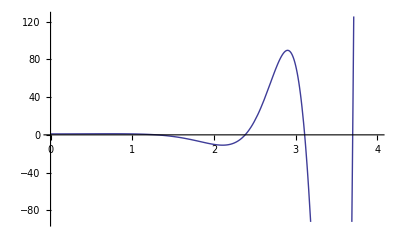

```mathematica
Plot[eigsol[x],{x,0,4}]
```

```mathematica
Table[FindRoot[eigsol[x]==0,{x,6+i/100}],{i,1,100}]
```

{{x→5.44674},{x→5.44674},{x→3.10938},{x→6.13734},{x→6.45499},{x→6.13734},{x→6.13734},{x→6.13734},{x→6.13734},{x→6.13734},{x→6.13734},{x→6.13734},{x→6.13734},{x→6.13734},{x→6.13734},{x→6.13734},{x→6.13734},{x→6.13734},{x→6.13734},{x→6.13734},{x→6.13734},{x→6.13734},{x→6.13734},{x→6.13734},{x→6.13734},{x→6.13734},{x→6.13734},{x→6.13734},{x→6.13734},{x→6.13734},{x→6.13734},{x→6.13734},{x→5.44674},{x→5.80232},{x→5.06627},{x→6.45499},{x→6.45499},{x→6.45499},{x→6.45499},{x→6.45499},{x→6.45499},{x→6.45499},{x→6.45499},{x→6.45499},{x→6.45499},{x→6.45499},{x→6.45499},{x→6.45499},{x→6.45499},{x→6.45499},{x→6.45499},{x→6.45499},{x→6.45499},{x→6.45499},{x→6.45499},{x→6.45499},{x→6.45499},{x→6.45499},{x→6.45499},{x→6.45499},{x→6.45499},{x→6.45499},{x→6.45499},{x→6.13734},{x→6.13734},{x→4.20326},{x→6.75773},{x→6.75773},{x→6.75773},{x→6.75773},{x→6.75773},{x→6.75773},{x→6.75773},{x→6.75773},{x→6.75773},{x→6.75773},{x→6.75773},{x→6.75773},{x→6.75773},{x→6.75773},{x→6.75773},{x→6.75773},{x→6.75773},{x→6.75773},{x→6.75773},{x→6.75773},{x→6.75773},{x→6.75773},{x→6.75773},{x→6.75773},{x→6.75773},{x→6.75773},{x→6.75773},{x→6.45499},{x→5.80232},{x→7.04747},{x→7.04747},{x→7.04747},{x→7.04747},{x→7.04747}}

```mathematica
eig={1.296763402567712,2.38114622522328,3.10937975527442,3.696980043577128,4.203257494533186,4.654804542010845,5.06627047109941,5.446744077399425,5.802324195412259,6.137338548284962}
```

{1.29676,2.38115,3.10938,3.69698,4.20326,4.6548,5.06627,5.44674,5.80232,6.13734}

```mathematica
realsol1
```

ⅇ^(-1/2 m^2 x^2) Hypergeometric1F1[1/4-m^2/4,1/2,m^2 x^2]

```mathematica
NIntegrate[(1-x^2)(realsol1/.{m->eig[[1]]})*(realsol1/.{m->eig[[2]]}),{x,-1,1}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {2.76990133638922`*^-15}. NIntegrate obtained 9.95731×10^-16 and 4.09182×10^-13 for the integral and error estimates.

0.

```mathematica
coeff1=Table[NIntegrate[(1-x^2)(realsol1/.{m->eig[[i]]}),{x,-1,1}],{i,1,10}]
```

{1.0108,-0.236852,0.12667,-0.0845003,0.062607,-0.0493316,0.0404793,-0.0341835,0.0294921,-0.0258705}

```mathematica
coeff2=Table[NIntegrate[(1-x^2)(realsol1/.{m->eig[[i]]})^2,{x,-1,1}],{i,1,10}]
```

{0.841753,0.791721,0.78762,0.786513,0.786064,0.78584,0.785713,0.785633,0.78558,0.785543}

```mathematica
coeff=Table[coeff1[[i]]/coeff2[[i]],{i,1,10}]
```

{1.20083,-0.299161,0.160826,-0.107437,0.0796461,-0.0627757,0.0515192,-0.0435107,0.0375418,-0.0329333}

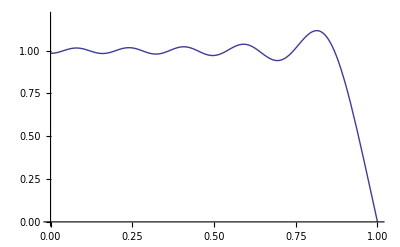

```mathematica
Plot[Sum[coeff[[i]]realsol1/.{m->eig[[i]]},{i,1,10}],{x,0,1},PlotRange->{{0,1},{0,1.2}}]
```

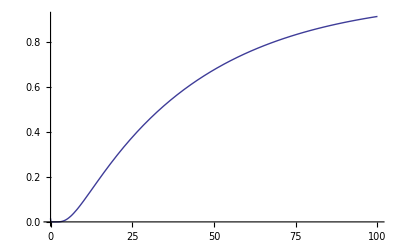

```mathematica
Plot[1-Sum[Exp[-eig[[i]]^4*y/108]coeff[[i]]realsol1/.{m->eig[[i]],x->0},{i,1,10}],{y,0,100}]
```

```mathematica
realsol1
```

ⅇ^(-1/2 m^2 x^2) Hypergeometric1F1[1/4-m^2/4,1/2,m^2 x^2]

```mathematica
N[Hypergeometric1F1[1,1,10]]
```

22026.5

```mathematica
N[Hypergeometric1F1[3,4,-6]]
```

0.0260564

```mathematica
whole=1-Sum[Exp[-eig[[i]]^4*y/108]coeff[[i]]realsol1/.{m->eig[[i]]},{i,1,10}]
```

1+0.0329333 ⅇ^(-18.8335 x^2-13.137 y) Hypergeometric1F1[-9.16673,1/2,37.6669 x^2]-0.0375418 ⅇ^(-16.8335 x^2-10.495 y) Hypergeometric1F1[-8.16674,1/2,33.667 x^2]+0.0435107 ⅇ^(-14.8335 x^2-8.14937 y) Hypergeometric1F1[-7.16676,1/2,29.667 x^2]-0.0515192 ⅇ^(-12.8335 x^2-6.1 y) Hypergeometric1F1[-6.16677,1/2,25.6671 x^2]+0.0627757 ⅇ^(-10.8336 x^2-4.34692 y) Hypergeometric1F1[-5.1668,1/2,21.6672 x^2]-0.0796461 ⅇ^(-8.83369 x^2-2.89015 y) Hypergeometric1F1[-4.16684,1/2,17.6674 x^2]+0.107437 ⅇ^(-6.83383 x^2-1.72968 y) Hypergeometric1F1[-3.16692,1/2,13.6677 x^2]-0.160826 ⅇ^(-4.83412 x^2-0.865508 y) Hypergeometric1F1[-2.16706,1/2,9.66824 x^2]+0.299161 ⅇ^(-2.83493 x^2-0.29766 y) Hypergeometric1F1[-1.16746,1/2,5.66986 x^2]-1.20083 ⅇ^(-0.840798 x^2-0.026183 y) Hypergeometric1F1[-0.170399,1/2,1.6816 x^2]